```mathematica
P[x_]=Exp[-x^2/(2 σ^2)]/(√(2 π) σ)
Integrate[P[x],{x,-∞,∞},Assumptions->σ>0]
```

(ⅇ^(-x^2/(2 σ^2)))/(√(2 π) σ)

1

```mathematica
σ=. ; 
Integrate[v P[v*Cos[θ]]*P[v*Sin[θ]],{θ,0,2π},{v,0,∞},Assumptions->σ>0]
```

1

```mathematica
Integrate[v P[v*Cos[θ]]*P[v*Sin[θ]],{θ,0,2π},Assumptions->σ>0]
```

(ⅇ^(-v^2/(2 σ^2)) v)/σ^2

1.29099

1

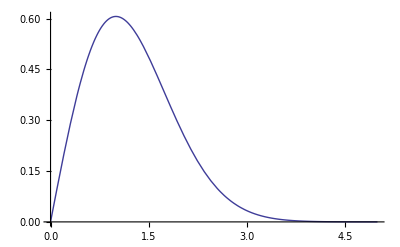

```mathematica
σ=Sqrt[0.1/0.06]
σ=1
Plot[(ⅇ^(-v^2/(2 σ^2)))/σ^2 v,{v,0,5}]
```

```mathematica
σ=.
Integrate[v P[v*Cos[θ]]*P[v*Sin[θ]] v^2 ,{v,0,∞},{θ,0,2π},Assumptions->σ>0]
```

2 σ^2